```mathematica
data=Import["/home/s3377910/HiggsScan/compare_fs/pole_masses_xt"];
```

```mathematica
cleanData=Cases[data,Except[{__,0}]];
```

```mathematica
{ms,ma2,tanBeta,at}=DeleteDuplicates/@Table[cleanData[[All,k]],{k,1,4}];
```

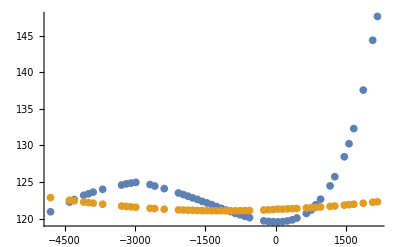

```mathematica
ListPlot[{Cases[cleanData,{ms[[1]],ma2[[1]],tanBeta[[1]],at_,mhEFT_,_}:>{-at-ms[[1]]/tanBeta[[1]],mhEFT}],Cases[cleanData,{ms[[1]],ma2[[1]],tanBeta[[1]],at_,_,mhFS_}:>{-at-ms[[1]]/tanBeta[[1]],mhFS}]},PlotRange->Full]
```

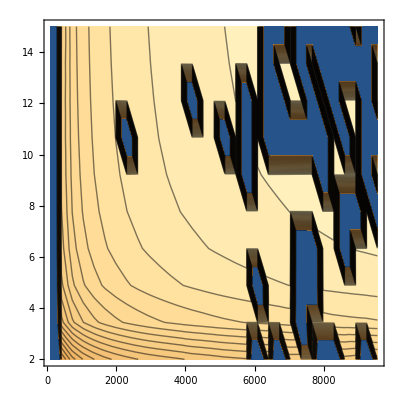

```mathematica
ListContourPlot[Cases[data,{ms_,ma2[[1]],tb_,mhEFT_,_}:>{ms,tb,mhEFT}],Contours->Table[3k,{k,20,50}]]
```

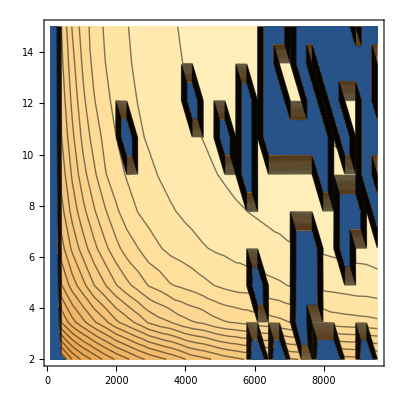

```mathematica
ListContourPlot[Cases[data,{ms_,ma2[[1]],tb_,mhEFT_,mhFS_}:>{ms,tb,mhFS}],Contours->Table[3k,{k,20,50}]]
```